```mathematica
(*Data*)
nperiods = 200;
μ=3.9877848 10^14;
Mp=1000;
l=50000;
a=6870000;
τ = 0;


period = 2 π √(a^3/μ);
ranget = nperiods*period;

psiQ =τ ;


(*Position vectorc and linear kinetic energy (translation of centre of mass)*)
rm[t] = ({{rc[t] Cos[θ[t]]}, {rc[t] Sin[θ[t]]}, {0}});
rp1[t]=rm[t]+({{l Cos[ψ[t]+θ[t]]}, {l  Sin[ψ[t]+θ[t]]}, {0}});
rp2[t]=rm[t]-({{l Cos[ψ[t]+θ[t]]}, {l  Sin[ψ[t]+θ[t]]}, {0}});

rm'[t]=D[rm[t], t];
rp1'[t]=D[rp1[t], t];
rp2'[t]=D[rp2[t], t];

Subscript[T, lin]=1/2 (2*Mp) (rc'[t]^2+rc[t]^2 θ'[t]^2);

(*Rotational kinetic energy (rotation of system about centre of mass)*)
ω[t]=({{0}, {0}, {(θ'[t]+ψ'[t])}});

Subscript[ⅈ, 123]=({{0, 0, 0}, {0, 2 Mp l^2, 0}, {0, 0, 2 Mp l^2}});

Subscript[T, rot]=1/2 Transpose[ω[t]].Subscript[ⅈ, 123].ω[t];

T=Subscript[T, lin]+Subscript[T, rot];

(*potential energy*)
Subscript[U, p1]=-(μ Mp)/(√(Transpose[rp1[t]].rp1[t]));
Subscript[U, p2]=-(μ Mp)/(√(Transpose[rp2[t]].rp2[t]));
V=Subscript[U, p1]+Subscript[U, p2];

L=T-V;
eqn1=Simplify[D[D[L, ψ'[t]], t]-D[L, ψ[t]]-psiQ];
eqn2 = Simplify[D[D[L, θ'[t]], t]-D[L, θ[t]]];
eqn3 = Simplify[D[D[L, rc'[t]], t]-D[L, rc[t]]];
```

```mathematica
motorisedBiffunc[e_]:=(

psi0 = 0.5;
psidsh0 =0;

r0 = a (1-e);
rdsh0 = 0;

theta0 = 0;
thetadsh0=1/r0*√((μ (1+e))/(a (1-e)))  ;

system=NDSolve[{eqn1==0,eqn2==0,eqn3==0,
ψ[0]==psi0,ψ'[0]==psidsh0, θ[0] == theta0,θ'[0]==thetadsh0,rc[0] == r0,rc'[0]==0},
{ψ,θ,rc},{t,0,ranget},
MaxSteps->∞,AccuracyGoal->Automatic];
psis[t_]:=ψ[t]/.system[[1]];
psidhs[t_]:=ψ'[t]/.system[[1]];

)
```

0.

0.0003

0.0006

0.0009

0.0012

0.0015

0.0018

0.0021

0.0024

0.0027

0.003

0.0033

0.0036

0.0039

0.0042

0.0045

0.0048

0.0051

0.0054

0.0057

0.006

0.0063

0.0066

0.0069

0.0072

0.0075

0.0078

0.0081

0.0084

0.0087

0.009

0.0093

0.0096

0.0099

0.0102

0.0105

0.0108

0.0111

0.0114

0.0117

0.012

0.0123

0.0126

0.0129

0.0132

0.0135

0.0138

0.0141

0.0144

0.0147

0.015

0.0153

0.0156

0.0159

0.0162

0.0165

0.0168

0.0171

0.0174

0.0177

0.018

0.0183

0.0186

0.0189

0.0192

0.0195

0.0198

0.0201

0.0204

0.0207

0.021

0.0213

0.0216

0.0219

0.0222

0.0225

0.0228

0.0231

0.0234

0.0237

0.024

0.0243

0.0246

0.0249

0.0252

0.0255

0.0258

0.0261

0.0264

0.0267

0.027

0.0273

0.0276

0.0279

0.0282

0.0285

0.0288

0.0291

0.0294

0.0297

0.03

0.0303

0.0306

0.0309

0.0312

0.0315

0.0318

0.0321

0.0324

0.0327

0.033

0.0333

0.0336

0.0339

0.0342

0.0345

0.0348

0.0351

0.0354

0.0357

0.036

0.0363

0.0366

0.0369

0.0372

0.0375

0.0378

0.0381

0.0384

0.0387

0.039

0.0393

0.0396

0.0399

0.0402

0.0405

0.0408

0.0411

0.0414

0.0417

0.042

0.0423

0.0426

0.0429

0.0432

0.0435

0.0438

0.0441

0.0444

0.0447

0.045

0.0453

0.0456

0.0459

0.0462

0.0465

0.0468

0.0471

0.0474

0.0477

0.048

0.0483

0.0486

0.0489

0.0492

0.0495

0.0498

0.0501

0.0504

0.0507

0.051

0.0513

0.0516

0.0519

0.0522

0.0525

0.0528

0.0531

0.0534

0.0537

0.054

0.0543

0.0546

0.0549

0.0552

0.0555

0.0558

0.0561

0.0564

0.0567

0.057

0.0573

0.0576

0.0579

0.0582

0.0585

0.0588

0.0591

0.0594

0.0597

0.06

0.0603

0.0606

0.0609

0.0612

0.0615

0.0618

0.0621

0.0624

0.0627

0.063

0.0633

0.0636

0.0639

0.0642

0.0645

0.0648

0.0651

0.0654

0.0657

0.066

0.0663

0.0666

0.0669

0.0672

0.0675

0.0678

0.0681

0.0684

0.0687

0.069

0.0693

0.0696

0.0699

0.0702

0.0705

0.0708

0.0711

0.0714

0.0717

0.072

0.0723

0.0726

0.0729

0.0732

0.0735

0.0738

0.0741

0.0744

0.0747

0.075

0.0753

0.0756

0.0759

0.0762

0.0765

0.0768

0.0771

0.0774

0.0777

0.078

0.0783

0.0786

0.0789

0.0792

0.0795

0.0798

0.0801

0.0804

0.0807

0.081

0.0813

0.0816

0.0819

0.0822

0.0825

0.0828

0.0831

0.0834

0.0837

0.084

0.0843

0.0846

0.0849

0.0852

0.0855

0.0858

0.0861

0.0864

0.0867

0.087

0.0873

0.0876

0.0879

0.0882

0.0885

0.0888

0.0891

0.0894

0.0897

0.09

0.0903

0.0906

0.0909

0.0912

0.0915

0.0918

0.0921

0.0924

0.0927

0.093

0.0933

0.0936

0.0939

0.0942

0.0945

0.0948

0.0951

0.0954

0.0957

0.096

0.0963

0.0966

0.0969

0.0972

0.0975

0.0978

0.0981

0.0984

0.0987

0.099

0.0993

0.0996

0.0999

0.1002

0.1005

0.1008

0.1011

0.1014

0.1017

0.102

0.1023

0.1026

0.1029

0.1032

0.1035

0.1038

0.1041

0.1044

0.1047

0.105

0.1053

0.1056

0.1059

0.1062

0.1065

0.1068

0.1071

0.1074

0.1077

0.108

0.1083

0.1086

0.1089

0.1092

0.1095

0.1098

0.1101

0.1104

0.1107

0.111

0.1113

0.1116

0.1119

0.1122

0.1125

0.1128

0.1131

0.1134

0.1137

0.114

0.1143

0.1146

0.1149

0.1152

0.1155

0.1158

0.1161

0.1164

0.1167

0.117

0.1173

0.1176

0.1179

0.1182

0.1185

0.1188

0.1191

0.1194

0.1197

0.12

0.1203

0.1206

0.1209

0.1212

0.1215

0.1218

0.1221

0.1224

0.1227

0.123

0.1233

0.1236

0.1239

0.1242

0.1245

0.1248

0.1251

0.1254

0.1257

0.126

0.1263

0.1266

0.1269

0.1272

0.1275

0.1278

0.1281

0.1284

0.1287

0.129

0.1293

0.1296

0.1299

0.1302

0.1305

0.1308

0.1311

0.1314

0.1317

0.132

0.1323

0.1326

0.1329

0.1332

0.1335

0.1338

0.1341

0.1344

0.1347

0.135

0.1353

0.1356

0.1359

0.1362

0.1365

0.1368

0.1371

0.1374

0.1377

0.138

0.1383

0.1386

0.1389

0.1392

0.1395

0.1398

0.1401

0.1404

0.1407

0.141

0.1413

0.1416

0.1419

0.1422

0.1425

0.1428

0.1431

0.1434

0.1437

0.144

0.1443

0.1446

0.1449

0.1452

0.1455

0.1458

0.1461

0.1464

0.1467

0.147

0.1473

0.1476

0.1479

0.1482

0.1485

0.1488

0.1491

0.1494

0.1497

0.15

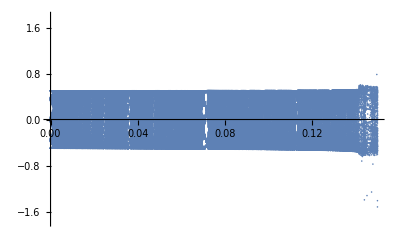

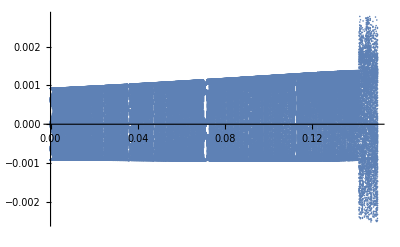

```mathematica
step = 0.0003;
emax = 0.15;
psistable = {};
psivstable={};
Do[Print[e];motorisedBiffunc[e];Do[psistable=Append[psistable,{e,psis[n*period]}];psivstable=Append[psivstable,{e,psidhs[n*period]}],{n,0,nperiods,1}],{e,0,emax,step}]
ListPlot[psistable]
ListPlot[psivstable]
```

```mathematica
points = {};
Do[points= Append[points,{}];points[[j]]=psistable[[j;;-1;;nperiods+1]],{j,1,nperiods}]
```

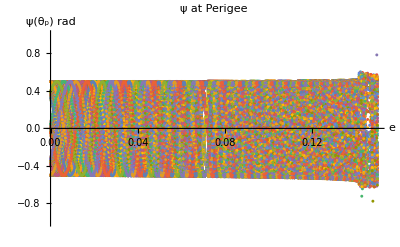

```mathematica
ListPlot[points,PlotMarkers->{•,3},PlotLabel->Style["ψ at Perigee",FontFamily->"Liberation Serif",35],AxesLabel->{Style["e",FontFamily->"Liberation Serif"],Style["ψ(θ_p) rad",FontFamily->"Liberation Serif"]},LabelStyle->Directive[Black,18,FontFamily->"Liberation Serif"],AxesOrigin->{0,0},ImageSize->{1080},PlotRange->{-1,1}]
```

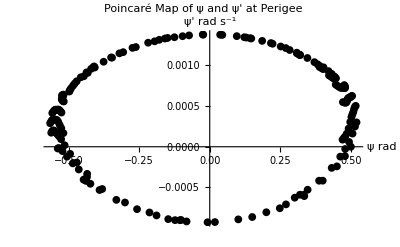

```mathematica
motorisedBiffunc[0.141];
newpoints = {};
Do[newpoints=Append[newpoints, {psis[period*n],psidhs[period*n]}],{n,0,nperiods,1}];
ListPlot[newpoints,PlotMarkers->{•,8},PlotLabel->Style["Poincaré Map of ψ and ψ' at Perigee\n",FontFamily->"Liberation Serif",35],PlotStyle->Black,AxesLabel->{Style["ψ rad",FontFamily->"Liberation Serif"],Style["ψ' rad s^-1",FontFamily->"Liberation Serif"]},LabelStyle->Directive[Black,18,FontFamily->"Liberation Serif"],AxesOrigin->{0,0},ImageSize->{1080}]
```